#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls"
```

/home/juanathan/Documentos/MSc_Thesis/3-FEM-Calc/3-Incrusted

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->colors}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,colors[[i]]],{i,10}]}
```

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
graphsOptsDensity := { BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> True, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None  }
graphsOptsDensityExport :={PlotLegends->None,FrameTicks->None, BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> False, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None}
```

#### Sorting Functions

```mathematica
maxPair[list_,ind_]:= SortBy[list, #[[ind]]&][[-1,{1,ind}]]
makePairs[list_,ind_]:=Map[Table[#[[;;,{1,i}]],{i,ind}]&,list]
```

Near Field Abs S

```mathematica
radius = 12.5;

cases = {7,6,5,1,2,3,4};
cases = Join @@ (7*#+cases &/@ Range[0,3]);
data = FileNames["2*csv","*s"];
data = data[[cases]];
Partition[data,7]//Transpose//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
limData = radius*3.5;
lim = radius*3;
```

Internal-s/2-Near-15-p75.csv | Internal-s/2-Near-38-p75.csv | Internal-s/2-Near-42-p75.csv | Internal-s/2-Near-75-p75.csv
Internal-s/2-Near-15-p50.csv | Internal-s/2-Near-38-p50.csv | Internal-s/2-Near-42-p50.csv | Internal-s/2-Near-75-p50.csv
Internal-s/2-Near-15-p25.csv | Internal-s/2-Near-38-p25.csv | Internal-s/2-Near-42-p25.csv | Internal-s/2-Near-75-p25.csv
Internal-s/2-Near-15-00.csv | Internal-s/2-Near-38-00.csv | Internal-s/2-Near-42-00.csv | Internal-s/2-Near-75-00.csv
Internal-s/2-Near-15-m25.csv | Internal-s/2-Near-38-m25.csv | Internal-s/2-Near-42-m25.csv | Internal-s/2-Near-75-m25.csv
Internal-s/2-Near-15-m50.csv | Internal-s/2-Near-38-m50.csv | Internal-s/2-Near-42-m50.csv | Internal-s/2-Near-75-m50.csv
Internal-s/2-Near-15-m75.csv | Internal-s/2-Near-38-m75.csv | Internal-s/2-Near-42-m75.csv | Internal-s/2-Near-75-m75.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = ConstantArray[-1,Length[data]]; (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {-x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<limData && Abs[#[[2]]]<limData) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<limData && Abs[#[[2]]]<limData) &],{i,Length[dataY]}];
```

11.0171

```mathematica
case = Flatten[Table[i,{4},{i,.75,-.75,-.25}],1];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]} &/@ case;

plotsX = MapThread[ListDensityPlot[#1, PlotRange->{{-1,1}*lim,{-1,1}*lim,{0,1}}, ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}];
plotsX = Partition[plotsX,7];
plotsY = MapThread[ListDensityPlot[#1, PlotRange->{{-1,1}*lim,{-1,1}*lim,{0,1}}, ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}];
plotsY = Partition[plotsY,7];
```

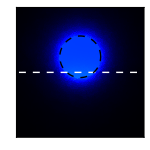
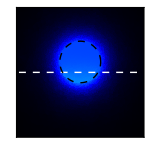
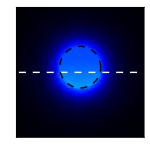
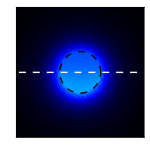
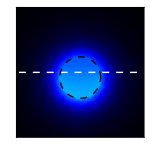
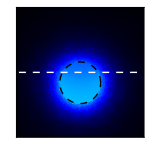
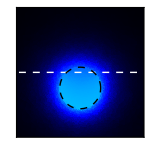
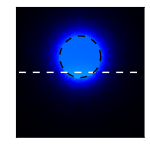
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
case = Flatten[Table[i,{4},{i,.75,-.75,-.25}],1];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]} &/@ case;

plotsX = MapThread[ListDensityPlot[#1, PlotRange->{{-1,1}*lim,{-1,1}*lim,{0,1}}, ColorFunctionScaling->False,Evaluate[graphsOptsDensityExport], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}];
plotsX = Partition[plotsX,7]
plotsY = MapThread[ListDensityPlot[#1, PlotRange->{{-1,1}*lim,{-1,1}*lim,{0,1}}, ColorFunctionScaling->False,Evaluate[graphsOptsDensityExport], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}];
plotsY = Partition[plotsY,7]
```

```mathematica
legends = {0,0};
legends[[1]] = Plot[x, {x, 0, max}, BaseStyle -> texStyle, 
  FrameTicks -> {{None, None}, {Automatic, None}},
  FrameStyle -> Black,    Frame-> True,
  AspectRatio -> 1/30, 
  PlotRange -> All, PlotRangePadding -> None, 
 ImageSize -> {60, 25/2}*4]
 
legends[[2]] =  DensityPlot[x, {x, 0,max}, {y, 0, 1}, BaseStyle -> texStyle, 
  FrameTicks -> {{None, None}, {None, None}},
  FrameStyle -> Black, 
  AspectRatio -> 1/30, 
  PlotRange -> All, ColorFunction -> JetExtended, 
  PlotPoints -> 40, PlotRangePadding -> None, 
 ImageSize -> {60, 25/2}*4]
```

-Graphics-

-Graphics-

```mathematica
MapIndexed[Export[FileNameJoin[{"Internal-sp","3-Near-S","Legend"<>{".pdf",".svg"}[[First[#2]]]}],#1]&,legends]

angle = ToString/@ {15,38,42,75}
MapIndexed[( name = angle[[First[#2]]];
  name = FileNameJoin[{"Internal-sp","3-Near-S","3-Near-SY-"<>name,"3-Near-SY-"<>name<>"-"<>ToString[Last[#2]]<>".svg"}];
  Export[name,#1]
  )&,
plotsY,{2}]

MapIndexed[( name = angle[[First[#2]]];
  name = FileNameJoin[{"Internal-sp","3-Near-S","3-Near-SX-"<>name,"3-Near-SX-"<>name<>"-"<>ToString[Last[#2]]<>".svg"}];
  Export[name,#1]
  )&,
plotsX,{2}]
```

{Internal-sp/3-Near-S/Legend.pdf,Internal-sp/3-Near-S/Legend.svg}

{15,38,42,75}

{{Internal-sp/3-Near-S/3-Near-SY-15/3-Near-SY-15-1.svg,Internal-sp/3-Near-S/3-Near-SY-15/3-Near-SY-15-2.svg,Internal-sp/3-Near-S/3-Near-SY-15/3-Near-SY-15-3.svg,Internal-sp/3-Near-S/3-Near-SY-15/3-Near-SY-15-4.svg,Internal-sp/3-Near-S/3-Near-SY-15/3-Near-SY-15-5.svg,Internal-sp/3-Near-S/3-Near-SY-15/3-Near-SY-15-6.svg,Internal-sp/3-Near-S/3-Near-SY-15/3-Near-SY-15-7.svg},{Internal-sp/3-Near-S/3-Near-SY-38/3-Near-SY-38-1.svg,Internal-sp/3-Near-S/3-Near-SY-38/3-Near-SY-38-2.svg,Internal-sp/3-Near-S/3-Near-SY-38/3-Near-SY-38-3.svg,Internal-sp/3-Near-S/3-Near-SY-38/3-Near-SY-38-4.svg,Internal-sp/3-Near-S/3-Near-SY-38/3-Near-SY-38-5.svg,Internal-sp/3-Near-S/3-Near-SY-38/3-Near-SY-38-6.svg,Internal-sp/3-Near-S/3-Near-SY-38/3-Near-SY-38-7.svg},{Internal-sp/3-Near-S/3-Near-SY-42/3-Near-SY-42-1.svg,Internal-sp/3-Near-S/3-Near-SY-42/3-Near-SY-42-2.svg,Internal-sp/3-Near-S/3-Near-SY-42/3-Near-SY-42-3.svg,Internal-sp/3-Near-S/3-Near-SY-42/3-Near-SY-42-4.svg,Internal-sp/3-Near-S/3-Near-SY-42/3-Near-SY-42-5.svg,Internal-sp/3-Near-S/3-Near-SY-42/3-Near-SY-42-6.svg,Internal-sp/3-Near-S/3-Near-SY-42/3-Near-SY-42-7.svg},{Internal-sp/3-Near-S/3-Near-SY-75/3-Near-SY-75-1.svg,Internal-sp/3-Near-S/3-Near-SY-75/3-Near-SY-75-2.svg,Internal-sp/3-Near-S/3-Near-SY-75/3-Near-SY-75-3.svg,Internal-sp/3-Near-S/3-Near-SY-75/3-Near-SY-75-4.svg,Internal-sp/3-Near-S/3-Near-SY-75/3-Near-SY-75-5.svg,Internal-sp/3-Near-S/3-Near-SY-75/3-Near-SY-75-6.svg,Internal-sp/3-Near-S/3-Near-SY-75/3-Near-SY-75-7.svg}}

{{Internal-sp/3-Near-S/3-Near-SX-15/3-Near-SX-15-1.svg,Internal-sp/3-Near-S/3-Near-SX-15/3-Near-SX-15-2.svg,Internal-sp/3-Near-S/3-Near-SX-15/3-Near-SX-15-3.svg,Internal-sp/3-Near-S/3-Near-SX-15/3-Near-SX-15-4.svg,Internal-sp/3-Near-S/3-Near-SX-15/3-Near-SX-15-5.svg,Internal-sp/3-Near-S/3-Near-SX-15/3-Near-SX-15-6.svg,Internal-sp/3-Near-S/3-Near-SX-15/3-Near-SX-15-7.svg},{Internal-sp/3-Near-S/3-Near-SX-38/3-Near-SX-38-1.svg,Internal-sp/3-Near-S/3-Near-SX-38/3-Near-SX-38-2.svg,Internal-sp/3-Near-S/3-Near-SX-38/3-Near-SX-38-3.svg,Internal-sp/3-Near-S/3-Near-SX-38/3-Near-SX-38-4.svg,Internal-sp/3-Near-S/3-Near-SX-38/3-Near-SX-38-5.svg,Internal-sp/3-Near-S/3-Near-SX-38/3-Near-SX-38-6.svg,Internal-sp/3-Near-S/3-Near-SX-38/3-Near-SX-38-7.svg},{Internal-sp/3-Near-S/3-Near-SX-42/3-Near-SX-42-1.svg,Internal-sp/3-Near-S/3-Near-SX-42/3-Near-SX-42-2.svg,Internal-sp/3-Near-S/3-Near-SX-42/3-Near-SX-42-3.svg,Internal-sp/3-Near-S/3-Near-SX-42/3-Near-SX-42-4.svg,Internal-sp/3-Near-S/3-Near-SX-42/3-Near-SX-42-5.svg,Internal-sp/3-Near-S/3-Near-SX-42/3-Near-SX-42-6.svg,Internal-sp/3-Near-S/3-Near-SX-42/3-Near-SX-42-7.svg},{Internal-sp/3-Near-S/3-Near-SX-75/3-Near-SX-75-1.svg,Internal-sp/3-Near-S/3-Near-SX-75/3-Near-SX-75-2.svg,Internal-sp/3-Near-S/3-Near-SX-75/3-Near-SX-75-3.svg,Internal-sp/3-Near-S/3-Near-SX-75/3-Near-SX-75-4.svg,Internal-sp/3-Near-S/3-Near-SX-75/3-Near-SX-75-5.svg,Internal-sp/3-Near-S/3-Near-SX-75/3-Near-SX-75-6.svg,Internal-sp/3-Near-S/3-Near-SX-75/3-Near-SX-75-7.svg}}

Near Field Abs p

```mathematica
radius = 12.5;

cases = {7,6,5,1,2,3,4};
cases = Join @@ (7*#+cases &/@ Range[0,3]);
data = FileNames["2*csv","*p"];
data = data[[cases]];
Partition[data,7]//Transpose//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
limData = radius*3.5;
lim = radius*3;
```

Internal-p/2-Near-15-p75.csv | Internal-p/2-Near-38-p75.csv | Internal-p/2-Near-42-p75.csv | Internal-p/2-Near-75-p75.csv
Internal-p/2-Near-15-p50.csv | Internal-p/2-Near-38-p50.csv | Internal-p/2-Near-42-p50.csv | Internal-p/2-Near-75-p50.csv
Internal-p/2-Near-15-p25.csv | Internal-p/2-Near-38-p25.csv | Internal-p/2-Near-42-p25.csv | Internal-p/2-Near-75-p25.csv
Internal-p/2-Near-15-00.csv | Internal-p/2-Near-38-00.csv | Internal-p/2-Near-42-00.csv | Internal-p/2-Near-75-00.csv
Internal-p/2-Near-15-m25.csv | Internal-p/2-Near-38-m25.csv | Internal-p/2-Near-42-m25.csv | Internal-p/2-Near-75-m25.csv
Internal-p/2-Near-15-m50.csv | Internal-p/2-Near-38-m50.csv | Internal-p/2-Near-42-m50.csv | Internal-p/2-Near-75-m50.csv
Internal-p/2-Near-15-m75.csv | Internal-p/2-Near-38-m75.csv | Internal-p/2-Near-42-m75.csv | Internal-p/2-Near-75-m75.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = ConstantArray[-1,Length[data]]; (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {-x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<limData && Abs[#[[2]]]<limData) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<limData && Abs[#[[2]]]<limData) &],{i,Length[dataY]}];
```

12.4446

```mathematica
case = Flatten[Table[i,{4},{i,.75,-.75,-.25}],1];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]} &/@ case;

plotsX = MapThread[ListDensityPlot[#1, PlotRange->{{-1,1}*lim,{-1,1}*lim,{0,1}}, ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}];
plotsX = Partition[plotsX,7];
plotsY = MapThread[ListDensityPlot[#1, PlotRange->{{-1,1}*lim,{-1,1}*lim,{0,1}}, ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}];
plotsY = Partition[plotsY,7];
```

```mathematica
case = Flatten[Table[i,{4},{i,.75,-.75,-.25}],1];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]} &/@ case;

plotsX = MapThread[ListDensityPlot[#1, PlotRange->{{-1,1}*lim,{-1,1}*lim,{0,1}}, ColorFunctionScaling->False,Evaluate[graphsOptsDensityExport], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}];
plotsX = Partition[plotsX,7]
plotsY = MapThread[ListDensityPlot[#1, PlotRange->{{-1,1}*lim,{-1,1}*lim,{0,1}}, ColorFunctionScaling->False,Evaluate[graphsOptsDensityExport], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}];
plotsY = Partition[plotsY,7]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
legends = {0,0};
legends[[1]] = Plot[x, {x, 0, max}, BaseStyle -> texStyle, 
  FrameTicks -> {{None, None}, {Automatic, None}},
  FrameStyle -> Black,    Frame-> True,
  AspectRatio -> 1/30, 
  PlotRange -> All, PlotRangePadding -> None, 
 ImageSize -> {60, 25/2}*4]
 
legends[[2]] =  DensityPlot[x, {x, 0,max}, {y, 0, 1}, BaseStyle -> texStyle, 
  FrameTicks -> {{None, None}, {None, None}},
  FrameStyle -> Black, 
  AspectRatio -> 1/30, 
  PlotRange -> All, ColorFunction -> JetExtended, 
  PlotPoints -> 40, PlotRangePadding -> None, 
 ImageSize -> {60, 25/2}*4]
```

-Graphics-

-Graphics-

```mathematica
MapIndexed[Export[FileNameJoin[{"Internal-sp","4-Near-P","Legend"<>{".pdf",".svg"}[[First[#2]]]}],#1]&,legends]

angle = ToString/@ {15,38,42,75}
MapIndexed[( name = angle[[First[#2]]];
  name = FileNameJoin[{"Internal-sp","4-Near-P","4-Near-PY-"<>name,"4-Near-PY-"<>name<>"-"<>ToString[Last[#2]]<>".svg"}];
  Export[name,#1]
  )&,
plotsY,{2}]

MapIndexed[( name = angle[[First[#2]]];
  name = FileNameJoin[{"Internal-sp","4-Near-P","4-Near-PX-"<>name,"4-Near-PX-"<>name<>"-"<>ToString[Last[#2]]<>".svg"}];
  Export[name,#1]
  )&,
plotsX,{2}]
```

{Internal-sp/4-Near-P/Legend.pdf,Internal-sp/4-Near-P/Legend.svg}

{15,38,42,75}

{{Internal-sp/4-Near-P/4-Near-PY-15/4-Near-PY-15-1.svg,Internal-sp/4-Near-P/4-Near-PY-15/4-Near-PY-15-2.svg,Internal-sp/4-Near-P/4-Near-PY-15/4-Near-PY-15-3.svg,Internal-sp/4-Near-P/4-Near-PY-15/4-Near-PY-15-4.svg,Internal-sp/4-Near-P/4-Near-PY-15/4-Near-PY-15-5.svg,Internal-sp/4-Near-P/4-Near-PY-15/4-Near-PY-15-6.svg,Internal-sp/4-Near-P/4-Near-PY-15/4-Near-PY-15-7.svg},{Internal-sp/4-Near-P/4-Near-PY-38/4-Near-PY-38-1.svg,Internal-sp/4-Near-P/4-Near-PY-38/4-Near-PY-38-2.svg,Internal-sp/4-Near-P/4-Near-PY-38/4-Near-PY-38-3.svg,Internal-sp/4-Near-P/4-Near-PY-38/4-Near-PY-38-4.svg,Internal-sp/4-Near-P/4-Near-PY-38/4-Near-PY-38-5.svg,Internal-sp/4-Near-P/4-Near-PY-38/4-Near-PY-38-6.svg,Internal-sp/4-Near-P/4-Near-PY-38/4-Near-PY-38-7.svg},{Internal-sp/4-Near-P/4-Near-PY-42/4-Near-PY-42-1.svg,Internal-sp/4-Near-P/4-Near-PY-42/4-Near-PY-42-2.svg,Internal-sp/4-Near-P/4-Near-PY-42/4-Near-PY-42-3.svg,Internal-sp/4-Near-P/4-Near-PY-42/4-Near-PY-42-4.svg,Internal-sp/4-Near-P/4-Near-PY-42/4-Near-PY-42-5.svg,Internal-sp/4-Near-P/4-Near-PY-42/4-Near-PY-42-6.svg,Internal-sp/4-Near-P/4-Near-PY-42/4-Near-PY-42-7.svg},{Internal-sp/4-Near-P/4-Near-PY-75/4-Near-PY-75-1.svg,Internal-sp/4-Near-P/4-Near-PY-75/4-Near-PY-75-2.svg,Internal-sp/4-Near-P/4-Near-PY-75/4-Near-PY-75-3.svg,Internal-sp/4-Near-P/4-Near-PY-75/4-Near-PY-75-4.svg,Internal-sp/4-Near-P/4-Near-PY-75/4-Near-PY-75-5.svg,Internal-sp/4-Near-P/4-Near-PY-75/4-Near-PY-75-6.svg,Internal-sp/4-Near-P/4-Near-PY-75/4-Near-PY-75-7.svg}}

{{Internal-sp/4-Near-P/4-Near-PX-15/4-Near-PX-15-1.svg,Internal-sp/4-Near-P/4-Near-PX-15/4-Near-PX-15-2.svg,Internal-sp/4-Near-P/4-Near-PX-15/4-Near-PX-15-3.svg,Internal-sp/4-Near-P/4-Near-PX-15/4-Near-PX-15-4.svg,Internal-sp/4-Near-P/4-Near-PX-15/4-Near-PX-15-5.svg,Internal-sp/4-Near-P/4-Near-PX-15/4-Near-PX-15-6.svg,Internal-sp/4-Near-P/4-Near-PX-15/4-Near-PX-15-7.svg},{Internal-sp/4-Near-P/4-Near-PX-38/4-Near-PX-38-1.svg,Internal-sp/4-Near-P/4-Near-PX-38/4-Near-PX-38-2.svg,Internal-sp/4-Near-P/4-Near-PX-38/4-Near-PX-38-3.svg,Internal-sp/4-Near-P/4-Near-PX-38/4-Near-PX-38-4.svg,Internal-sp/4-Near-P/4-Near-PX-38/4-Near-PX-38-5.svg,Internal-sp/4-Near-P/4-Near-PX-38/4-Near-PX-38-6.svg,Internal-sp/4-Near-P/4-Near-PX-38/4-Near-PX-38-7.svg},{Internal-sp/4-Near-P/4-Near-PX-42/4-Near-PX-42-1.svg,Internal-sp/4-Near-P/4-Near-PX-42/4-Near-PX-42-2.svg,Internal-sp/4-Near-P/4-Near-PX-42/4-Near-PX-42-3.svg,Internal-sp/4-Near-P/4-Near-PX-42/4-Near-PX-42-4.svg,Internal-sp/4-Near-P/4-Near-PX-42/4-Near-PX-42-5.svg,Internal-sp/4-Near-P/4-Near-PX-42/4-Near-PX-42-6.svg,Internal-sp/4-Near-P/4-Near-PX-42/4-Near-PX-42-7.svg},{Internal-sp/4-Near-P/4-Near-PX-75/4-Near-PX-75-1.svg,Internal-sp/4-Near-P/4-Near-PX-75/4-Near-PX-75-2.svg,Internal-sp/4-Near-P/4-Near-PX-75/4-Near-PX-75-3.svg,Internal-sp/4-Near-P/4-Near-PX-75/4-Near-PX-75-4.svg,Internal-sp/4-Near-P/4-Near-PX-75/4-Near-PX-75-5.svg,Internal-sp/4-Near-P/4-Near-PX-75/4-Near-PX-75-6.svg,Internal-sp/4-Near-P/4-Near-PX-75/4-Near-PX-75-7.svg}}